```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
```

```mathematica
Subscript[D, 1]=44 10^-3; (*meters*)
Subscript[D, 2]=60 10^-3 ; (*meters*)
Subscript[D, 3]=30  10^-3; (*meters*)

Subscript[r, 1]=Subscript[D, 1]/2; (*meters*)
Subscript[r, 2]=Subscript[D, 2]/2 ; (*meters*)
Subscript[r, 3]=Subscript[D, 3]/2; (*meters*)

Subscript[J, 1]=(π ((Subscript[r, 2])^4-(Subscript[r, 1])^4))/2 (*meters^4*);
Subscript[J, 2]=(π (Subscript[r, 2])^4)/2 (*meters^4*);
Subscript[J, 3]=(π (Subscript[r, 3])^4)/2 (*meters^4*);

ClearAll[J]

J[X_]:=Piecewise[
{{Subscript[J, 1],0≤ X<0.6},
{Subscript[J, 2],0.6≤ X<0.8},
{Subscript[J, 3],0.8≤ X<1.2}}
] (*meters^4*)

T[X_]:=Piecewise[
{{2250,0≤ X<0.8},
{250,0.8≤ X<1.2}}
] (*meters^4*);

G=77 10^9 (*N/m^2 or Pa*);
L=1.2  (*in meters*);

Subscript[θ, L]=1/G Integrate[T[X]/J[X],{X,0,1.2}]
Subscript[θ, L]/Degree
```

0.0403109

2.30964

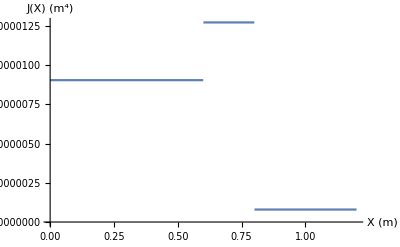

```mathematica
Plot[J[X],{X,0,1.2},AxesLabel->{"X (m)","J(X) (m^4)"}]
```

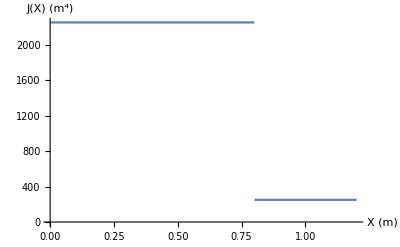

```mathematica
Plot[T[X],{X,0,1.2},AxesLabel->{"X (m)","J(X) (m^4)"}]
```